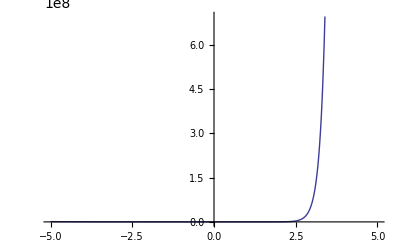

1.+6. x+18. x^2+378.429 x^3+1243.29 (-1+x) x^3

{1.,1.,1.,403.429,403.429}

{1.,1.,1.,403.429,403.429}

```mathematica
(*f[x_]:=1/(3+x);
X = {};
Do [X = Append[X,3+0.5*i], {i, 0, 6}]*)

f[x_]=N[E]^(6x);
X={0,0,0,1,1};

n=Length[X];
Y=f[X];
R=ConstantArray[0,{n,n}];
R[[All,1]]=Y;
i=2;
While[i≤n,k=i;While[k≤n,If[X[[k]]-X[[k-i+1]]≠0,R[[k,i]]=(R[[k,i-1]]-R[[k-1,i-1]])/(X[[k]]-X[[k-i+1]]),R[[k,i]]=(D[f[x],{x,i-1}]/.x->X[[k]])/Factorial[i-1]];k=k+1];i=i+1];
pn[x_]=Sum[R[[i]][[i]]Product[x-X[[k]],{k,i-1}],{i,n}];
Plot[Abs[f[x]-pn[x]],{x,-5,5}]
pn[x]
pn[X]
f[X]
```